*Note that torusVectors, torusRatio, and torusDensity takes a while to execute.

```mathematica
-Graphics-;
```

In order to cover the moduli space with globally dense packings, we need to look at what happens in the regions in the moduli space where free circles exist.  We can do this by taking the two edge cases, the purple edge above the red region and the blue line above the yellow region and taking these packings and simply extending the length of the lattice vector w1 or w2.  In this document, we will look at the region that is encapsulated above the red region, which is found by extending the packings that are on the purple line (the blue line that is directly above the red region).  Notice that really this region extends to infinity in the moduli space.

We start off by taking the centers of the embedding V3E5L1N1T31 as below.

```mathematica
centers = Simplify[{{0,0},

{1/4 (1-√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))+Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))+2 Cos[β] √(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))))),1/2 ((√(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))))) Sin[β]+Cos[β] (((√(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))))-√(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))))) Cot[β]+(-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))) Sin[β]))},{1/4 (3+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))+2 Cos[β] √(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))))),1/2 (√(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))))) Sin[β]-1/2 Cos[β] ((-(√(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))))+√(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))))) Cot[β]+(-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))) Sin[β])}




}];
```

Then we take the lattice vectors of the embedding V3E5L1N1T31.  However, note that we take the longer lattice vector, in this case w2 and scale it by some factor s.

```mathematica
latticeVectors = Simplify[{
 {1,0},
{ s((√(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))))*Cos[β]),s((√(-1+2 √2+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β]))-Cos[2 β] (-1+√((-5+4 √2+Cos[2 β])/(-1+Cos[2 β])))))*Sin[β])}}];
```

Also, to allow free circles, we need to break some of the edges.  These are the remaining edges we keep so that we can visualize the packing.

```mathematica
edges = {{1,2,0,0},{1,1,1,0},{2,3,0,0},{3,1,1,0}};
```

Now, we need to set bounds on s; 1 is an obvious lower bound.  Now, really this region should continue up in the moduli space.  However, to be practice, and also to create a good picture, the longest length is when the x=1/2.  In other words, we want the maximum length to be the same as the scaled version of V3E6L1N2T11.  So, using basic trigonometry, we get the following upper bound.

```mathematica
Simplify[1/(2*Cos[(1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4)+Pi/4]*((2/Sqrt[2])*Cos[1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])-Pi/4]))]
```

1/2 (1+√2) Csc[π/4+ArcTan[(-1+√2)/(√(-1+2 √2))]]

```mathematica
Manipulate[
Graphics[
Translate[
Union[
Table[{Thick,Dashing[1],Black,Line[{centers[[edges[[i,1]] ]],centers[[edges[[i,2]] ]]+
edges[[i,3]]*latticeVectors[[1]]+
edges[[i,4]]*latticeVectors[[2]]}/.{s->a,β->b}]},{i,1,Length[edges]}],(*Edges*)
{{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[1]]/.{s->a,β->b} }]},{Thick,Dashed,Blue,Arrow[{{0,0},latticeVectors[[2]]/.{s->a,β->b}}]}},(*Fundamental Domain*)
{{AbsolutePointSize[5],Point[centers/.{s->a,β->b}]}},(*Circle Centers*)
Table[Text[Style[i,Medium],centers[[i]]/.{s->a,β->b},Offset[{10,-30},{0,0}]],{i,1,Length[centers]}],(*Label Circle Centers*)
{{Opacity[.5],EdgeForm[Thick],LightOrange,Disk[centers[[1]]/.{s->a,β->b},1/2]},
{Opacity[.5],EdgeForm[Thick],LightGreen,Disk[centers[[2]]/.{s->a,β->b},1/2*(Sqrt[2]-1)]},
{Opacity[.5],EdgeForm[Thick],LightRed,Disk[centers[[3]]/.{s->a,β->b},1/2*(Sqrt[2]-1)]}}, (*Circles*){{Text[Style["s",Small],centers[[2]]/.{s->a,β->b},Offset[{0,10},{0,0}]]},
{Text[Style["β",Small],centers[[3]]/.{s->a,β->b},Offset[{10,-10},{0,0}]]}}(*Angle Markers Labels*)

], Flatten[Table[i*latticeVectors[[1]]+j*latticeVectors[[2]],{i,-2,2,1},{j,-2,2,1}]/.{s->a,β->b},1] (*List of the translation vectors*)
],PlotRange-> {{-1,3},{-1,3}} (*Restrict the plot window*)
],{{b,Pi/2,"β"},1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]),Pi/2},{{a,1,"s"},1,1/2 (1+√2) Csc[π/4+ArcTan[(-1+√2)/(√(-1+2 √2))]]}
]
```

```mathematica
torusAngleFromVectors = FullSimplify[VectorAngle[latticeVectors[[1]],latticeVectors[[2]]],{Element[{β},Reals],s≥1,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])≤β≤Pi/2}]
```

$Aborted

```mathematica
torusRatio = FullSimplify[EuclideanDistance[{0,0},latticeVectors[[2]]]/EuclideanDistance[{0,0},latticeVectors[[1]]],{Element[{β},Reals],s≥1,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])≤β≤Pi/2}]
```

s √Abs[-1+2 √2+√(1-2 (-1+√2) Csc[β]^2)-Cos[2 β] (-1+√(1-2 (-1+√2) Csc[β]^2))]

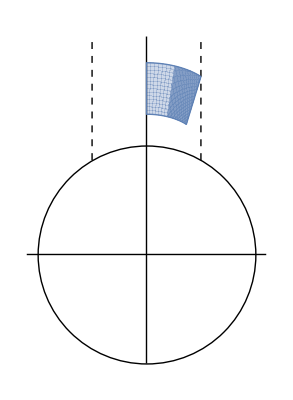

```mathematica
Show[Graphics[Circle[{0,0},1]],
Graphics[Line[{{0,-1},{0,2}}]],
Graphics[Line[{{-1.1,0},{1.1,0}}]],
Graphics[{Dashed,Thick,Line[{{-.5,Sqrt[3]/2},{-.5,2}}]}],
Graphics[{Dashed,Thick,Line[{{.5,Sqrt[3]/2},{.5,2}}]}],
ParametricPlot[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])]},{β,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]),Pi/2},{s,1,1/2 (1+√2) Csc[π/4+ArcTan[(-1+√2)/(√(-1+2 √2))]]}]

]
```

## Density Of Packings

Here we analyze the density of the locally maximally dense packings and explore the density.

```mathematica
torusDensity = FullSimplify[(Pi*(1/2)^2+2*Pi*(1/2(Sqrt[2]-1))^2)/(Norm[latticeVectors[[1]]]*Norm[latticeVectors[[2]]]*Sin[torusAngleFromVectors]) ,{Element[{β},Reals],s≥1,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))])≤β≤Pi/2}]
```

((7-4 √2) π)/(4 s √(Abs[-1+2 √2+√(1-2 (-1+√2) Csc[β]^2)-Cos[2 β] (-1+√(1-2 (-1+√2) Csc[β]^2))]-Conjugate[√(-1+2 √2+Cos[2 β]+√((-1+Cos[2 β]) (-5+4 √2+Cos[2 β])))]^2 Cos[β]^2))

```mathematica
Show[
ParametricPlot3D[{Re[(torusRatio*Exp[I torusAngleFromVectors])],Im[(torusRatio*Exp[I torusAngleFromVectors])],torusDensity},{β,1/2 (π-2 ArcTan[(-1+√2)/(√(-1+2 √2))]),Pi/2},{s,1,1/2 (1+√2) Csc[π/4+ArcTan[(-1+√2)/(√(-1+2 √2))]]}]

]
```

-Graphics3D-